## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
primes=Table[Prime[x]^(15-1), {x,10000}];
```

```mathematica
n=15;results={};
```

## Prime 15

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv15=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv15];
```

```mathematica
count = Total[adj]//Counts
```

<|303→14,203→5,205→7,453→1,477→2,507→1,508→1,301→3,525→1,302→6,522→2,530→1,298→1,554→1,520→1,591→1,539→1,589→1,579→1,608→1,569→1,304→2,606→1,294→1,600→1,633→1,305→2,626→2,308→3,631→1,644→1,306→2,649→1,310→1,667→1,309→1,314→3,685→1,317→2,689→1,315→1,322→2,678→1,319→1,676→1,320→2,706→1,321→1,733→1,324→1,328→1,452→1,329→1,285→1,747→1,331→1,335→2,734→1,323→1,776→1,342→1,341→1,300→1,348→1,336→1,761→1,354→1,349→1,787→1,352→1,353→1,351→1,365→1,807→1,363→2,297→1,350→1,370→1,366→1,817→1,378→1,376→2,371→2,822→1,394→1,401→1,358→1,388→1,410→2,829→1,236→3,433→2,864→1,249→4,396→1,402→1,414→1,860→1,448→1,457→1,450→1,896→1,415→1,466→1,293→1,487→1,797→1,383→1,389→1,446→1,928→1,435→1,774→1,911→1,969→1,975→1,642→1,974→1,1010→1,1034→1,1050→1,1030→1,803→1,1045→1,1053→1,1132→1,1140→1,697→1,1148→1,1150→1,1191→1,1195→1,1176→1,1219→1,1268→1,780→1,1293→1,1357→1,715→1,1333→1,1341→1,1332→1,1337→1,1391→1,1389→1,1430→1,1412→1,1427→1,1446→1,1483→1,1595→1,1611→1,1531→1,972→1,1652→1,1651→1,1188→1,1674→1,1714→1,1770→1,1775→1,1837→1,1920→1,1604→1,1928→1,1167→1,1924→1,1992→1,1987→1,2041→1,1863→1,1712→1,2033→1,2036→1,2047→1,2066→1,2122→1,2143→1,2215→1,2300→1,2311→1,2322→1,2334→1,2465→1,2100→1,2446→1,2491→1,2569→1,1973→1,2792→1,2383→1,2908→1,2947→1,2879→1,2326→1,2951→1,3030→1,1706→1,2993→1,3045→1,3099→1,3233→1,3260→1,3248→1,3453→1,3503→1,3554→1,3424→1,3547→1,3743→1,3394→1,3760→1,3852→1,3885→1,3914→1,1253→1,3901→1,3943→1,3964→1,3941→1,3971→1,4113→1,4104→1,4171→1,4196→1,4407→1,4413→1,4388→1,4465→1,4481→1,4526→1,4548→1,4587→1,4604→1,4597→1,4618→1,4714→1,4745→1,4824→1,4920→1,4728→1,4947→1,4949→1,4942→1,5010→1,5143→1,5273→1,4768→1,5152→1,5283→1,5342→1,5356→1,5589→1,4816→1,5695→1,4201→1,5651→1,5953→1,5948→1,6206→1,6104→1,6196→1,6381→1,6366→1,6362→1,6717→1,6877→1,199→8,210→3,208→6,207→9,206→8,197→6,195→9,194→11,287→1,200→6,201→4,202→4,284→1,198→4,279→1,278→1,276→1,273→1,274→1,192→11,272→1,268→2,269→1,270→1,267→3,196→10,262→2,265→1,263→1,188→11,260→1,193→7,258→1,256→3,254→1,253→2,255→2,191→4,190→10,185→2,247→3,189→8,251→1,186→5,248→2,184→4,244→4,204→4,238→7,241→2,246→1,242→2,243→1,245→2,239→4,183→6,182→3,233→2,237→1,235→2,179→15,231→2,180→9,226→4,229→1,176→16,224→4,230→1,225→8,228→3,178→9,223→2,177→7,227→3,181→6,175→7,221→6,187→6,174→7,218→6,219→3,222→3,220→4,216→4,172→12,217→7,171→11,213→6,215→7,173→8,209→4,212→4,170→6,211→6,169→8,214→3,168→8,165→9,167→8,163→9,164→15,141→29,153→13,151→21,142→16,143→13,161→15,160→12,159→14,155→20,148→13,162→10,149→14,146→16,144→9,158→9,150→12,145→10,138→13,140→16,147→14,166→4,139→19,157→12,152→20,156→12,154→23,136→12,137→22,135→24,134→12,133→18,131→23,132→19,125→22,130→14,129→13,123→24,128→14,120→19,124→14,121→19,108→25,116→32,114→35,110→21,126→10,112→32,111→23,119→13,118→24,127→8,109→28,117→29,115→25,113→20,106→37,122→14,107→23,105→26,104→25,102→30,101→22,103→21,100→17,95→21,99→18,97→25,93→25,91→37,98→17,86→47,94→21,88→42,90→36,85→41,92→32,87→40,96→19,84→47,89→36,83→42,80→66,81→49,82→57,79→68,78→49,77→69,75→55,74→35,76→75,73→35,68→51,69→51,72→36,67→60,71→51,66→47,70→48,64→56,65→68,62→51,61→58,59→52,63→53,57→42,60→53,58→39,54→31,56→36,55→25,53→26,49→60,48→52,45→46,52→33,44→45,51→34,47→49,37→22,46→48,50→52,40→36,33→47,41→29,43→33,34→45,39→32,32→57,38→26,30→43,28→46,23→77,36→32,29→47,35→35,19→80,42→30,31→41,22→63,24→47,25→65,27→37,26→49,17→107,18→93,12→123,21→81,20→60,16→108,15→127,14→125,13→119,10→169,9→163,7→281,5→468,8→203,11→163,6→346,4→595,3→752,2→438|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{303,14/9999},{203,5/9999},{205,7/9999},{453,1/9999},{477,2/9999},{507,1/9999},{508,1/9999},{301,1/3333},{525,1/9999},{302,2/3333},{522,2/9999},{530,1/9999},{298,1/9999},{554,1/9999},{520,1/9999},{591,1/9999},{539,1/9999},{589,1/9999},{579,1/9999},{608,1/9999},{569,1/9999},{304,2/9999},{606,1/9999},{294,1/9999},{600,1/9999},{633,1/9999},{305,2/9999},{626,2/9999},{308,1/3333},{631,1/9999},{644,1/9999},{306,2/9999},{649,1/9999},{310,1/9999},{667,1/9999},{309,1/9999},{314,1/3333},{685,1/9999},{317,2/9999},{689,1/9999},{315,1/9999},{322,2/9999},{678,1/9999},{319,1/9999},{676,1/9999},{320,2/9999},{706,1/9999},{321,1/9999},{733,1/9999},{324,1/9999},{328,1/9999},{452,1/9999},{329,1/9999},{285,1/9999},{747,1/9999},{331,1/9999},{335,2/9999},{734,1/9999},{323,1/9999},{776,1/9999},{342,1/9999},{341,1/9999},{300,1/9999},{348,1/9999},{336,1/9999},{761,1/9999},{354,1/9999},{349,1/9999},{787,1/9999},{352,1/9999},{353,1/9999},{351,1/9999},{365,1/9999},{807,1/9999},{363,2/9999},{297,1/9999},{350,1/9999},{370,1/9999},{366,1/9999},{817,1/9999},{378,1/9999},{376,2/9999},{371,2/9999},{822,1/9999},{394,1/9999},{401,1/9999},{358,1/9999},{388,1/9999},{410,2/9999},{829,1/9999},{236,1/3333},{433,2/9999},{864,1/9999},{249,4/9999},{396,1/9999},{402,1/9999},{414,1/9999},{860,1/9999},{448,1/9999},{457,1/9999},{450,1/9999},{896,1/9999},{415,1/9999},{466,1/9999},{293,1/9999},{487,1/9999},{797,1/9999},{383,1/9999},{389,1/9999},{446,1/9999},{928,1/9999},{435,1/9999},{774,1/9999},{911,1/9999},{969,1/9999},{975,1/9999},{642,1/9999},{974,1/9999},{1010,1/9999},{1034,1/9999},{1050,1/9999},{1030,1/9999},{803,1/9999},{1045,1/9999},{1053,1/9999},{1132,1/9999},{1140,1/9999},{697,1/9999},{1148,1/9999},{1150,1/9999},{1191,1/9999},{1195,1/9999},{1176,1/9999},{1219,1/9999},{1268,1/9999},{780,1/9999},{1293,1/9999},{1357,1/9999},{715,1/9999},{1333,1/9999},{1341,1/9999},{1332,1/9999},{1337,1/9999},{1391,1/9999},{1389,1/9999},{1430,1/9999},{1412,1/9999},{1427,1/9999},{1446,1/9999},{1483,1/9999},{1595,1/9999},{1611,1/9999},{1531,1/9999},{972,1/9999},{1652,1/9999},{1651,1/9999},{1188,1/9999},{1674,1/9999},{1714,1/9999},{1770,1/9999},{1775,1/9999},{1837,1/9999},{1920,1/9999},{1604,1/9999},{1928,1/9999},{1167,1/9999},{1924,1/9999},{1992,1/9999},{1987,1/9999},{2041,1/9999},{1863,1/9999},{1712,1/9999},{2033,1/9999},{2036,1/9999},{2047,1/9999},{2066,1/9999},{2122,1/9999},{2143,1/9999},{2215,1/9999},{2300,1/9999},{2311,1/9999},{2322,1/9999},{2334,1/9999},{2465,1/9999},{2100,1/9999},{2446,1/9999},{2491,1/9999},{2569,1/9999},{1973,1/9999},{2792,1/9999},{2383,1/9999},{2908,1/9999},{2947,1/9999},{2879,1/9999},{2326,1/9999},{2951,1/9999},{3030,1/9999},{1706,1/9999},{2993,1/9999},{3045,1/9999},{3099,1/9999},{3233,1/9999},{3260,1/9999},{3248,1/9999},{3453,1/9999},{3503,1/9999},{3554,1/9999},{3424,1/9999},{3547,1/9999},{3743,1/9999},{3394,1/9999},{3760,1/9999},{3852,1/9999},{3885,1/9999},{3914,1/9999},{1253,1/9999},{3901,1/9999},{3943,1/9999},{3964,1/9999},{3941,1/9999},{3971,1/9999},{4113,1/9999},{4104,1/9999},{4171,1/9999},{4196,1/9999},{4407,1/9999},{4413,1/9999},{4388,1/9999},{4465,1/9999},{4481,1/9999},{4526,1/9999},{4548,1/9999},{4587,1/9999},{4604,1/9999},{4597,1/9999},{4618,1/9999},{4714,1/9999},{4745,1/9999},{4824,1/9999},{4920,1/9999},{4728,1/9999},{4947,1/9999},{4949,1/9999},{4942,1/9999},{5010,1/9999},{5143,1/9999},{5273,1/9999},{4768,1/9999},{5152,1/9999},{5283,1/9999},{5342,1/9999},{5356,1/9999},{5589,1/9999},{4816,1/9999},{5695,1/9999},{4201,1/9999},{5651,1/9999},{5953,1/9999},{5948,1/9999},{6206,1/9999},{6104,1/9999},{6196,1/9999},{6381,1/9999},{6366,1/9999},{6362,1/9999},{6717,1/9999},{6877,1/9999},{199,8/9999},{210,1/3333},{208,2/3333},{207,1/1111},{206,8/9999},{197,2/3333},{195,1/1111},{194,1/909},{287,1/9999},{200,2/3333},{201,4/9999},{202,4/9999},{284,1/9999},{198,4/9999},{279,1/9999},{278,1/9999},{276,1/9999},{273,1/9999},{274,1/9999},{192,1/909},{272,1/9999},{268,2/9999},{269,1/9999},{270,1/9999},{267,1/3333},{196,10/9999},{262,2/9999},{265,1/9999},{263,1/9999},{188,1/909},{260,1/9999},{193,7/9999},{258,1/9999},{256,1/3333},{254,1/9999},{253,2/9999},{255,2/9999},{191,4/9999},{190,10/9999},{185,2/9999},{247,1/3333},{189,8/9999},{251,1/9999},{186,5/9999},{248,2/9999},{184,4/9999},{244,4/9999},{204,4/9999},{238,7/9999},{241,2/9999},{246,1/9999},{242,2/9999},{243,1/9999},{245,2/9999},{239,4/9999},{183,2/3333},{182,1/3333},{233,2/9999},{237,1/9999},{235,2/9999},{179,5/3333},{231,2/9999},{180,1/1111},{226,4/9999},{229,1/9999},{176,16/9999},{224,4/9999},{230,1/9999},{225,8/9999},{228,1/3333},{178,1/1111},{223,2/9999},{177,7/9999},{227,1/3333},{181,2/3333},{175,7/9999},{221,2/3333},{187,2/3333},{174,7/9999},{218,2/3333},{219,1/3333},{222,1/3333},{220,4/9999},{216,4/9999},{172,4/3333},{217,7/9999},{171,1/909},{213,2/3333},{215,7/9999},{173,8/9999},{209,4/9999},{212,4/9999},{170,2/3333},{211,2/3333},{169,8/9999},{214,1/3333},{168,8/9999},{165,1/1111},{167,8/9999},{163,1/1111},{164,5/3333},{141,29/9999},{153,13/9999},{151,7/3333},{142,16/9999},{143,13/9999},{161,5/3333},{160,4/3333},{159,14/9999},{155,20/9999},{148,13/9999},{162,10/9999},{149,14/9999},{146,16/9999},{144,1/1111},{158,1/1111},{150,4/3333},{145,10/9999},{138,13/9999},{140,16/9999},{147,14/9999},{166,4/9999},{139,19/9999},{157,4/3333},{152,20/9999},{156,4/3333},{154,23/9999},{136,4/3333},{137,2/909},{135,8/3333},{134,4/3333},{133,2/1111},{131,23/9999},{132,19/9999},{125,2/909},{130,14/9999},{129,13/9999},{123,8/3333},{128,14/9999},{120,19/9999},{124,14/9999},{121,19/9999},{108,25/9999},{116,32/9999},{114,35/9999},{110,7/3333},{126,10/9999},{112,32/9999},{111,23/9999},{119,13/9999},{118,8/3333},{127,8/9999},{109,28/9999},{117,29/9999},{115,25/9999},{113,20/9999},{106,37/9999},{122,14/9999},{107,23/9999},{105,26/9999},{104,25/9999},{102,10/3333},{101,2/909},{103,7/3333},{100,17/9999},{95,7/3333},{99,2/1111},{97,25/9999},{93,25/9999},{91,37/9999},{98,17/9999},{86,47/9999},{94,7/3333},{88,14/3333},{90,4/1111},{85,41/9999},{92,32/9999},{87,40/9999},{96,19/9999},{84,47/9999},{89,4/1111},{83,14/3333},{80,2/303},{81,49/9999},{82,19/3333},{79,68/9999},{78,49/9999},{77,23/3333},{75,5/909},{74,35/9999},{76,25/3333},{73,35/9999},{68,17/3333},{69,17/3333},{72,4/1111},{67,20/3333},{71,17/3333},{66,47/9999},{70,16/3333},{64,56/9999},{65,68/9999},{62,17/3333},{61,58/9999},{59,52/9999},{63,53/9999},{57,14/3333},{60,53/9999},{58,13/3333},{54,31/9999},{56,4/1111},{55,25/9999},{53,26/9999},{49,20/3333},{48,52/9999},{45,46/9999},{52,1/303},{44,5/1111},{51,34/9999},{47,49/9999},{37,2/909},{46,16/3333},{50,52/9999},{40,4/1111},{33,47/9999},{41,29/9999},{43,1/303},{34,5/1111},{39,32/9999},{32,19/3333},{38,26/9999},{30,43/9999},{28,46/9999},{23,7/909},{36,32/9999},{29,47/9999},{35,35/9999},{19,80/9999},{42,10/3333},{31,41/9999},{22,7/1111},{24,47/9999},{25,65/9999},{27,37/9999},{26,49/9999},{17,107/9999},{18,31/3333},{12,41/3333},{21,9/1111},{20,20/3333},{16,12/1111},{15,127/9999},{14,125/9999},{13,119/9999},{10,169/9999},{9,163/9999},{7,281/9999},{5,52/1111},{8,203/9999},{11,163/9999},{6,346/9999},{4,595/9999},{3,752/9999},{2,146/3333}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.131789/x^0.864846]

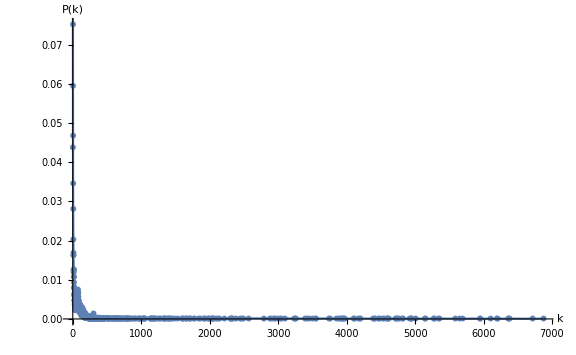

```mathematica
vis15=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv15]//Mean//N
```

101.093

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh15=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh15];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,2→3365,5→927,4→1558,6→653,3→2227,8→284,7→428,10→146,9→191,12→59,11→89,13→37,14→15,15→10,16→5,19→1,18→1,20→1,21→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,3365/9999},{5,103/1111},{4,1558/9999},{6,653/9999},{3,2227/9999},{8,284/9999},{7,428/9999},{10,146/9999},{9,191/9999},{12,59/9999},{11,89/9999},{13,37/9999},{14,5/3333},{15,10/9999},{16,5/9999},{19,1/9999},{18,1/9999},{20,1/9999},{21,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.06941/x^1.57755]

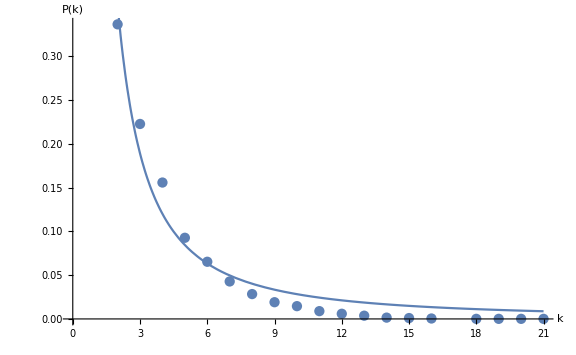

```mathematica
hvis15=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igh15]//Mean//N
```

3.93339

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,15,9999,101.093,0.864846 ± 0.0293598,0.131789 ± 0.00792231},{horizontal,15,9999,3.93339,1.57755 ± 0.20501,1.06941 ± 0.223943}}